# Flux Reconstruction (FR) & Correction Procedure via Reconstruction (CPR)

## by Manuel Diaz, NTU, 2013.08.20

Based on Ideas of jounal papers:

1. Z.J. Wang & Hai - Yang Gao, JCP 228 (2009) 8161-8186.
2. H.T. Huynh, AIAA (2007) 4079.
3. Jie Du, Chi-Wang Shu, MengPing Zhang, Brown University (2013) 15.

Derivation of the Method in one-dimensional space.

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

## Initialize Symbols & Notation

#### Change Notebook BackGround

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[u, j-1/2]^+];Symbolize[Subscript[u, j-1/2]^-];Symbolize[Subscript[f̂, j-1/2]];
```

```mathematica
Symbolize[Subscript[u, j+1/2]^-];Symbolize[Subscript[u, j+1/2]^+];Symbolize[Subscript[f̂, j+1/2]];
```

## Review on Flux Reconstruction Method

Define Domain x ∈ [ a , b ],
We then divide it into ‘n’ small cells

```mathematica
a= 0; b = 1; n = 10; nodes = n+1; Δx = (b-a)/n;
```

```mathematica
Table [Subscript[x, i-1/2]=a+ i Δx,{i,0,n}]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

Define Intervals I_j:

```mathematica
Table[Subscript[I, j]={Subscript[x, j-3/2],Subscript[x, j-1/2]},{j,1,n}]
```

{{0,1/10},{1/10,1/5},{1/5,3/10},{3/10,2/5},{2/5,1/2},{1/2,3/5},{3/5,7/10},{7/10,4/5},{4/5,9/10},{9/10,1}}

Define cell sizes h_j:

```mathematica
Table[Subscript[h, j]=(Subscript[x, j-1/2]-Subscript[x, j-3/2]),{j,1,n}]
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

Define cell centers x_j :

```mathematica
Table[Subscript[x, j]=(Subscript[x, j-3/2]+Subscript[x, j-1/2])/2,{j,1,n}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

Standar Element Definition I_ξ:

```mathematica
Subscript[I, ξ] = ({{-1, 1}})
```

{{-1,1}}

Define Solution Points ξ :
We can use for example: four-Gauss Legendre Points,

```mathematica
abscissas = {-√(1/35 (15+2 √30)),-√(1/35 (15-2 √30)),√(1/35 (15-2 √30)),√(1/35 (15+2 √30))}; 
weights={1/36 (18-√30),1/36 (18+√30),1/36 (18+√30),1/36 (18-√30)};
```

Or we can use also: four-Gauss-Lobatto Points,

```mathematica
(* abscissas = {-1,1/Sqrt[5],-1/Sqrt[5],1}; *)
(* weights={1/6,5/6,5/6,1/6}; *)
```

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}=abscissas; (* also the local coordinates inside Subscript[I, j] *)
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]}=weights;
```

Define Interpolation polynomial for every u_j:

```mathematica
StencilPoints[r_] := Table[{Subscript[ξ, j],Subscript[u, j]},{j,1,r}]
```

```mathematica
StencilPoints[4]
```

{{-√(1/35 (15+2 √30)),u_1},{-√(1/35 (15-2 √30)),u_2},{√(1/35 (15-2 √30)),u_3},{√(1/35 (15+2 √30)),u_4}}

```mathematica
LagrangePolynomials[r_] := Collect[InterpolatingPolynomial[StencilPoints[r],ξ],u,Simplify]
```

```mathematica
Subscript[u, j][ξ_]:=Evaluate[LagrangePolynomials[4]]
```

```mathematica
(* Testing *)
```

```mathematica
Subscript[u, j][-1]//N
```

0.0228218 (66.9005 u_1-35.6516 u_2+17.5605 u_3-4.9916 u_4)

```mathematica
Subscript[u, j][1]//N
```

0.0228218 (-4.9916 u_1+17.5605 u_2-35.6516 u_3+66.9005 u_4)

```mathematica
(* Everything seems ok in this part *)
```

Similarly for the flux values f_j :

```mathematica
StencilPoints[r_] := Table[{Subscript[ξ, j],Subscript[f, j]},{j,1,r}]
```

```mathematica
StencilPoints[4]
```

{{-√(1/35 (15+2 √30)),f_1},{-√(1/35 (15-2 √30)),f_2},{√(1/35 (15-2 √30)),f_3},{√(1/35 (15+2 √30)),f_4}}

```mathematica
LagrangePolynomials[r_] := Collect[InterpolatingPolynomial[StencilPoints[r],ξ],f,Simplify]
```

```mathematica
Subscript[f, j][ξ_]:=Evaluate[LagrangePolynomials[4]]
```

```mathematica
(* Testing *)
Subscript[f, j][-1]//N
```

0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)

```mathematica
Subscript[f, j][1]//N
```

0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)

```mathematica
(* Good! *)
```

This result comes from interpolating ‘u’ values over the selected gauss Lobatto/ Solution points. ( equations 2.2 and 2.3 in [1], equations 6, 7 and 11 in [3] )

Define Subpolynomial Domains over our original Domain. We  define the following mapping for x and ξ (abscissas here) :

```mathematica
Subscript[x, 𝒟]=Table[Subscript[x, j]+ (abscissas Subscript[h, j])/2,{j,1,n}];
Subscript[x, 𝒟]//TableForm//N
```

0.00694318 | 0.0330009 | 0.0669991 | 0.0930568
0.106943 | 0.133001 | 0.166999 | 0.193057
0.206943 | 0.233001 | 0.266999 | 0.293057
0.306943 | 0.333001 | 0.366999 | 0.393057
0.406943 | 0.433001 | 0.466999 | 0.493057
0.506943 | 0.533001 | 0.566999 | 0.593057
0.606943 | 0.633001 | 0.666999 | 0.693057
0.706943 | 0.733001 | 0.766999 | 0.793057
0.806943 | 0.833001 | 0.866999 | 0.893057
0.906943 | 0.933001 | 0.966999 | 0.993057

Define ' u_(j,k)’ values over the entire domain, Assume u(x) = 0.5 +sin(2πx), therefore

```mathematica
Subscript[u, 𝒟]=0.5+Sin[2 π Subscript[x, 𝒟]];
Subscript[u, 𝒟]//TableForm
```

0.543611 | 0.705868 | 0.908644 | 1.05194
1.12251 | 1.24175 | 1.36707 | 1.43667
1.46363 | 1.4943 | 1.4943 | 1.46363
1.43667 | 1.36707 | 1.24175 | 1.12251
1.05194 | 0.908644 | 0.705868 | 0.543611
0.456389 | 0.294132 | 0.0913564 | -0.0519436
-0.122508 | -0.241746 | -0.367068 | -0.436675
-0.463628 | -0.494301 | -0.494301 | -0.463628
-0.436675 | -0.367068 | -0.241746 | -0.122508
-0.0519436 | 0.0913564 | 0.294132 | 0.456389

```mathematica
Table[Subscript[u, j,k]= Subscript[u, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

Define ' f_(j,k)’  as the flux values, we can computet them at the solution points as well. Assume f(u) = u^2/2, therefore

```mathematica
Subscript[f, 𝒟]= Subscript[u, 𝒟]^2/2;
```

```mathematica
Subscript[f, 𝒟] //TableForm
```

0.147757 | 0.249125 | 0.412817 | 0.553293
0.630013 | 0.770966 | 0.934437 | 1.03202
1.0711 | 1.11647 | 1.11647 | 1.0711
1.03202 | 0.934437 | 0.770966 | 0.630013
0.553293 | 0.412817 | 0.249125 | 0.147757
0.104145 | 0.0432567 | 0.00417299 | 0.00134907
0.00750416 | 0.0292205 | 0.0673694 | 0.0953425
0.107476 | 0.122167 | 0.122167 | 0.107476
0.0953425 | 0.0673694 | 0.0292205 | 0.00750416
0.00134907 | 0.00417299 | 0.0432567 | 0.104145

```mathematica
Table[Subscript[f, j,k]= Subscript[f, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

At the boundary cells at ξ_1 and ξ_K (or ξ_4 for our example) immediatly we recognize them as (u_(j-1/2))^+= u_(j,1), and (u_(j+1/2))^-= u_(j,K)

To the right boundary of ‘ j+1/2’

```mathematica
SuperMinus[Subscript[u, j+1/2]] = Subscript[u, 𝒟][[All,4]];
SuperMinus[Subscript[u, j+1/2]] = Most[%];
SuperMinus[Subscript[u, j+1/2]] // TableForm
```

1.05194
1.43667
1.46363
1.12251
0.543611
-0.0519436
-0.436675
-0.463628
-0.122508

To the left boundary of ‘j+1/2’

```mathematica
SuperPlus[Subscript[u, j+1/2]] = Subscript[u, 𝒟][[All,1]];
SuperPlus[Subscript[u, j+1/2]] = Rest[SuperPlus[Subscript[u, j+1/2]]];
SuperPlus[Subscript[u, j+1/2]] // TableForm
```

1.12251
1.46363
1.43667
1.05194
0.456389
-0.122508
-0.463628
-0.436675
-0.0519436

Compute Reimann Fluxes at the boundary points (using Lax-Friedrichs flux),

```mathematica
f[u_]:= u^2/2; df [u_]:=u;
```

```mathematica
α[a_,b_]:= Max[df[a],df[b]]
```

```mathematica
LF[a_,b_]:= 1/2(α[a,b](a-b)+(f[a]+f[b]))
```

```mathematica
Subscript[f̂, j+1/2]=LF[SuperMinus[Subscript[u, j+1/2]],SuperPlus[Subscript[u, j+1/2]]]; 
Subscript[f̂, j+1/2]//TableForm
```

0.540012
1.03184
1.07129
0.643293
0.189782
0.056067
0.121134
0.0816842
-0.0472137

Based on Shu’s paper, the Continuous Flux Polynomial, F_j(ξ), must satisfy the following conditions:

1. The continuous Flux function F_j(ξ) is requiered to take the Riemann Fluxes at both end of the cell I_j, namely,
	F_j[-1] = (f̂)_(j-1/2)	and		F_j[1] =(f̂)_(j+1/2)
Here I’m using Lax-Friedrichs Flux Reimann Flux to solve for the discontinuity at the interface.

2. In each cell I_jthe degree of F_j(ξ), should be K, i.e., one order higher than the solution polynomial u_j(ξ).

3. F_j(ξ) is required to approximate the discontinuous flux function f_j(ξ) is some sense. Hence, F_j(ξ) - f_j(ξ) approximates the function 0.

The continuous Flux Polynomial is then defined as,

```mathematica
Subscript[F, j][ξ] = Subscript[f, j][ξ]+(Subscript[f̂, j-1/2]-Subscript[f, j][-1])Subscript[ℊ, LB][ξ]+(Subscript[f̂, j+1/2]-Subscript[f, j][1])Subscript[ℊ, RB][ξ] //N //TableForm
```

0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(0.540012-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]
0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(1.03184-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]
0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(1.07129-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]
0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(0.643293-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]
0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(0.189782-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]
0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(0.056067-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]
0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(0.121134-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]
0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(0.0816842-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]
0.0228218 (0.333333 (-12.1366+14.0938 ξ+105. ξ^2-121.932 ξ^3) f_1-0.047619 (-545.043+1603.16 ξ+735. ξ^2-2161.89 ξ^3) f_2+25.9545 f_3+76.3409 ξ f_3-35. ξ^2 f_3-102.947 ξ^3 f_3-4.04555 f_4-4.69792 ξ f_4+35. ξ^2 f_4+40.644 ξ^3 f_4)+((f̂)_(j-1/2)-0.0228218 (66.9005 f_1-35.6516 f_2+17.5605 f_3-4.9916 f_4)) ℊ_LB[ξ]+(-0.0472137-0.0228218 (-4.9916 f_1+17.5605 f_2-35.6516 f_3+66.9005 f_4)) ℊ_RB[ξ]

for every ξ ∈ [-1,1]. Last equation corresponds to equation 2.8 in [1] and equation 13 in [3].

The function ℊ_LB(x) is the correction at the left boundary satisfying
	ℊ_LB(-1) = 1,	ℊ_LB(1) = 0;

The function ℊ_RB(x) is the correction at the right boundary satisfying
	ℊ_RB(-1) = 0,	ℊ_RB(1) = 1;

Because of symmetry, we only need to consider ℊ_L(x), or simply ℊ(x). It is more convenient to consider the correction function in the standar element g(ξ) on [-1,1]. Using special Polynomials such as Radau and Legendre polynomials, the DG, SD (or SD/SV) methods can be succesfully recovered.

The order of our Lagrange Polynomial is 3rd degree, therefore we choose a 4th degree Legendre polynomial

```mathematica
ℊ[x_]:= LegendreP[4,x];ℊ[ξ]
```

1/8 (3-30 ξ^2+35 ξ^4)

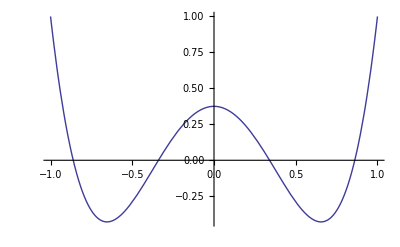

```mathematica
Plot[ℊ[x],{x,-1,1}]
```